```mathematica
datX=Import[NotebookDirectory[]<>"experimentData\\outputData_Pearlized Cotton Rib X.h5","Data"];
datY=Import[NotebookDirectory[]<>"experimentData\\outputData_Pearlized Cotton Rib Y.h5","Data"];
tNames={"/video1/traj","/video2/traj","/video3/traj","/video4/traj","/video5/traj"};
frameNames={"/video1/frames","/video2/frames","/video3/frames","/video4/frames","/video5/frames"};
forceNames={"/video1/forces","/video2/forces","/video3/forces","/video4/forces","/video5/forces"};

clampSize[dat_]:=dat["/clampSize"][[1]];
fabricSize[dat_]:=dat["/fabricSize"][[1]];
forceGaugeReading[dat_,k_]:=dat[forceNames[[k]]];
clampSizeInPhysicalUnits=35.5;(**^-3;*)
stress[dat_,k_]:=forceGaugeReading[dat,k]/fabricSize[dat](clampSize[dat]/clampSizeInPhysicalUnits);

(* Pin order by convention is: RLBT, clamp bottom, clamp top (if clamp dots present) *)
horizontalLength[dat_,k_]:=Sqrt[(dat[tNames[[k]]][[1,1,;;]]-dat[tNames[[k]]][[2,1,;;]])^2+(dat[tNames[[k]]][[1,2,;;]]-dat[tNames[[k]]][[2,2,;;]])^2];
verticalLength[dat_,k_]:=Sqrt[(dat[tNames[[k]]][[3,1,;;]]-dat[tNames[[k]]][[4,1,;;]])^2+(dat[tNames[[k]]][[3,2,;;]]-dat[tNames[[k]]][[4,2,;;]])^2];
clampLength[dat_,k_]:=Sqrt[(dat[tNames[[k]]][[5,1,;;]]-dat[tNames[[k]]][[6,1,;;]])^2+(dat[tNames[[k]]][[5,2,;;]]-dat[tNames[[k]]][[6,2,;;]])^2];

relExtensionToStrain[x_]:=(x^2-1)/2;

axialStrain[dat_,k_]:=relExtensionToStrain[clampLength[dat,k]/clampLength[dat,k][[1]]];
transverseStrain[dat_,k_]:=relExtensionToStrain[horizontalLength[dat,k]/horizontalLength[dat,k][[1]]];

(* For X sample, the horizontal length is Y, vertical length is X, and force is in X direction *)
Table[{stress[datX,k],0 stress[datX,k],axialStrain[datX,k],transverseStrain[datX,k]},{k,5}];
xdatFile=Flatten[Transpose/@%,1];
(* For Y sample, the horizontal length is X, vertical length is Y, and force is in Y direction *)
(* Reminder: Both x and y go in one file once we have them!*)
Table[{0 stress[datY,k],stress[datY,k],transverseStrain[datY,k],axialStrain[datY,k]},{k,5}];
ydatFile=Flatten[Transpose/@%,1];

datFile=Join[xdatFile,ydatFile];
TableView@datFile;
Export[NotebookDirectory[]<>"CottonRib.dat",datFile,"CSV"]
```

C:\Users\Sam\Documents\GitHub\uniaxial\CottonRib.dat

```mathematica
clampLength[datY,2];
```

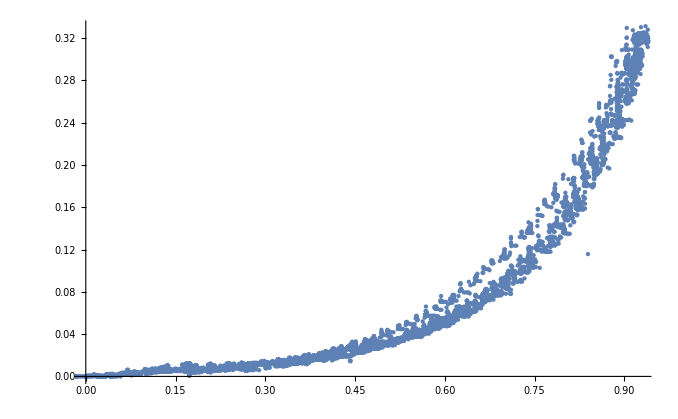

```mathematica
Show[Table[ListPlot[{relExtensionToStrain[clampLength[datY,k]/clampLength[datY,1][[1]]],stress[datY,k]}//Transpose],{k,5}]]
```

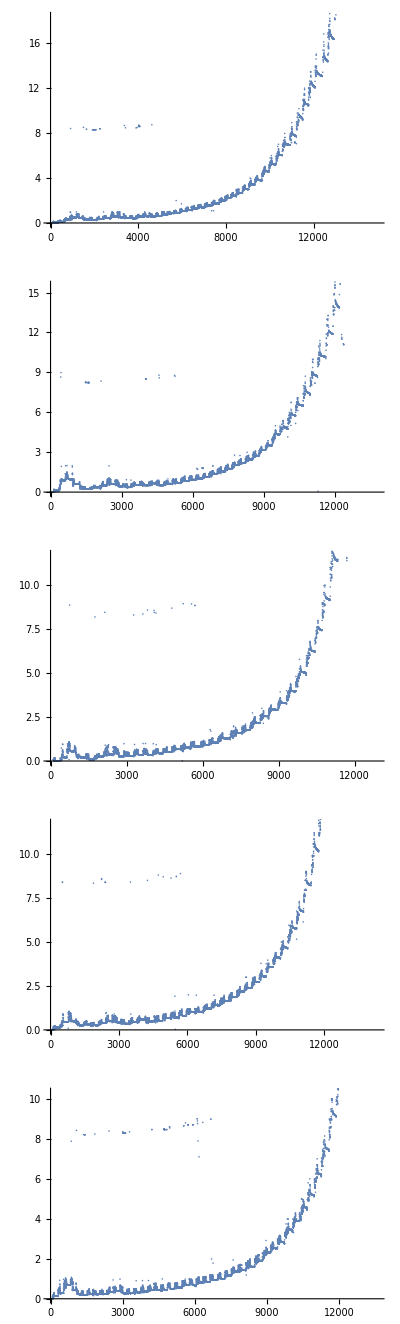

```mathematica
(* Demo: Force vs time data *)
GraphicsColumn[Table[ListPlot[{datX[frameNames[[k]]],datX[forceNames[[k]]]}//Transpose],{k,5}]]
```

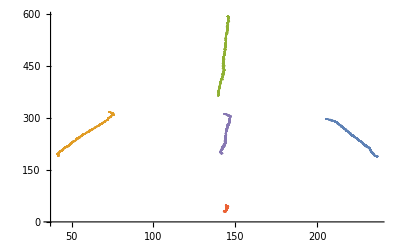

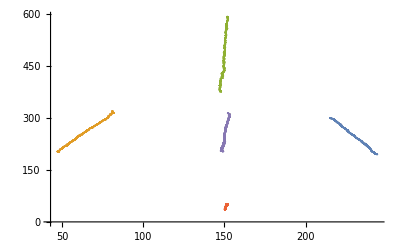

```mathematica
(* Demo: Pin order is consistent across videos! *)
ListPlot[Table[{dat[tNames[[3]]][[k,1,;;]],dat[tNames[[3]]][[k,2,;;]]}//Transpose,{k,5}]]
ListPlot[Table[{dat[tNames[[4]]][[k,1,;;]],dat[tNames[[4]]][[k,2,;;]]}//Transpose,{k,5}]]
```